# Fano resonance in a two-level quantum dot side-coupled to leads

## Authors: Woo-Ram Lee, Jaeuk U. Kim, and Heung-Sun Sim

## Publication: Physical Review B 77, 033305 (2008)

## Theory 1: two-level quantum dot side-coupled to leads

## Theory 2: electric current formula

## Theory 3: quantum dot Green’s function

cf.)

## Theory 4: Fano lineshape in conductance

## Code 1: Load packages

```mathematica
Needs["PlotLegends`"]
$TextStyle={FontFamily->Arial,FontSize->12}
```

{FontFamily→Arial,FontSize→12}

## Code 2: Set up parameters

```mathematica
T=0.000001;(*temperature*)
Γ=0.025;(*Energy Unit*)
Subscript[Γ, 1]=0.63*2Γ;(*level broadening for level 1*)
Subscript[Γ, 2]=0.37*2Γ;(*level broadening for level 2*)
Δ=1.6Γ;(*level separation*)
Subscript[ξ, 1]=0;(*energy for level 1*)
Subscript[ξ, 2]=Subscript[ξ, 1]+Δ;(*energy for level 2*)
ρ=0.5;(*flat density of states for electron reservoir*)
Subscript[t, LR]=0.3/(π ρ);(*tunneling matrix element for the direct channel between reservoir L and R*)
U=25Γ;(*interlevel Coulomb repulsion*)
```

## Code 3: Define functions

```mathematica
α[n1_,n2_]:=(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 1](Subscript[ξ, 2]-Subscript[ξ, 1]+U(n1-n2))+π ρ Subscript[t, LR](1+β);
β=Subscript[Γ, 2]/Subscript[Γ, 1];
q=(1-(π ρ Subscript[t, LR])^2)/(2 π ρ Subscript[t, LR]);

Subscript[Ξ, 1]=(-(π ρ Subscript[t, LR]+I)Subscript[Γ, 1])/(2(1+(π ρ Subscript[t, LR])^2));
Subscript[Ξ, 2]=(-(-π ρ Subscript[t, LR]+I)Subscript[Γ, 2])/(2(1+(π ρ Subscript[t, LR])^2));
n2[n1_]:=1/π ArcTan[(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 2](V-Subscript[ξ, 2]-U n1)-π ρ Subscript[t, LR]]+1/2;
g1[n1_]:=1/π ArcTan[(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 1](V-Subscript[ξ, 1]-U n2[n1])+π ρ Subscript[t, LR]]+1/2;
n1[n2_]:=1/π ArcTan[(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 1](V-Subscript[ξ, 1]-U n2)+π ρ Subscript[t, LR]]+1/2;
g2[n2_]:=1/π ArcTan[(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 2](V-Subscript[ξ, 2]-U n1[n2])-π ρ Subscript[t, LR]]+1/2;
x[V_,n2_]:=(2(1+(π ρ Subscript[t, LR])^2))/Subscript[Γ, 1](V-Subscript[ξ, 1]-U n2)+π ρ Subscript[t, LR];
G[V_,n1_,n2_]:=((2 π ρ Subscript[t, LR])/(1+(π ρ Subscript[t, LR])^2))^2((x[V,n2]^2-(α[n1,n2]+q(β-1))x[V,n2]-q α[n1,n2]+β)^2)/(((x[V,n2])^2+1)((x[V,n2]-α[n1,n2])^2+β^2));
```

## Code 4: Build up the list for conductance, level occupations, and occupation cross-correlation as a function of gate voltage

```mathematica
L=Table[{V/Γ,b1=bb1=N1=NN1=b2=bb2=N2=NN2={};A1=A2=B1=B2=w1=w2=0;
Do[a1=FindRoot[n1==g1[n1],{n1,p1}];If[Abs[g1[Replace[n1,a1]]-Replace[n1,a1]]<0.000001,bb1=Union[b1,{Replace[n1,a1]}]];b1=bb1,{p1,0,1,0.1}];bb1[[0]]=0;
Do[If[Abs[bb1[[i]]-bb1[[i-1]]]>0.000001,N1=Union[NN1,{bb1[[i]]}];NN1=N1],{i,1,Length[bb1]}];
Do[a2=FindRoot[n2==g2[n2],{n2,p2}];If[Abs[g2[Replace[n2,a2]]-Replace[n2,a2]]<0.000001,bb2=Union[b2,{Replace[n2,a2]}]];b2=bb2,{p2,0,1,0.1}];bb2[[0]]=0;
Do[If[Abs[bb2[[i]]-bb2[[i-1]]]>0.000001,N2=Union[NN2,{bb2[[i]]}];NN2=N2],{i,1,Length[bb2]}];
Do[w1=Exp[Im[Subscript[Ξ, 1]]/(π T)(1/2 Log[((Subscript[ξ, 1]-V+U n2[N1[[i]]]+ Re[Subscript[Ξ, 1]])^2+(Im[Subscript[Ξ, 1]])^2)/((d+Subscript[ξ, 1]-V+U n2[N1[[i]]]+ Re[Subscript[Ξ, 1]])^2+(Im[Subscript[Ξ, 1]])^2)]-(Subscript[ξ, 1]-V+U n2[N1[[i]]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]](ArcTan[(Subscript[ξ, 1]-V+U n2[N1[[i]]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]]]-ArcTan[(d+Subscript[ξ, 1]-V+U n2[N1[[i]]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]]]))+Im[Subscript[Ξ, 2]]/(π T)(1/2 Log[((Subscript[ξ, 2]-V+U N1[[i]]+ Re[Subscript[Ξ, 2]])^2+(Im[Subscript[Ξ, 2]])^2)/((d+Subscript[ξ, 2]-V+U N1[[i]]+ Re[Subscript[Ξ, 2]])^2+(Im[Subscript[Ξ, 2]])^2)]-(Subscript[ξ, 2]-V+U N1[[i]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]](ArcTan[(Subscript[ξ, 2]-V+U N1[[i]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]]]-ArcTan[(d+Subscript[ξ, 2]-V+U N1[[i]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]]]))];
A1+=N1[[i]]*w1;
B1+=w1,{i,1,Length[N1]}];A1/B1,
Do[w2=Exp[Im[Subscript[Ξ, 1]]/(π T)(1/2 Log[((Subscript[ξ, 1]-V+U N2[[i]]+ Re[Subscript[Ξ, 1]])^2+(Im[Subscript[Ξ, 1]])^2)/((d+Subscript[ξ, 1]-V+U N2[[i]]+ Re[Subscript[Ξ, 1]])^2+(Im[Subscript[Ξ, 1]])^2)]-(Subscript[ξ, 1]-V+U N2[[i]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]](ArcTan[(Subscript[ξ, 1]-V+U N2[[i]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]]]-ArcTan[(d+Subscript[ξ, 1]-V+U N2[[i]]+ Re[Subscript[Ξ, 1]])/Im[Subscript[Ξ, 1]]]))+Im[Subscript[Ξ, 2]]/(π T)(1/2 Log[((Subscript[ξ, 2]-V+U n1[N2[[i]]]+ Re[Subscript[Ξ, 2]])^2+(Im[Subscript[Ξ, 2]])^2)/((d+Subscript[ξ, 2]-V+U n1[N2[[i]]]+ Re[Subscript[Ξ, 2]])^2+(Im[Subscript[Ξ, 2]])^2)]-(Subscript[ξ, 2]-V+U n1[N2[[i]]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]](ArcTan[(Subscript[ξ, 2]-V+U n1[N2[[i]]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]]]-ArcTan[(d+Subscript[ξ, 2]-V+U n1[N2[[i]]]+ Re[Subscript[Ξ, 2]])/Im[Subscript[Ξ, 2]]]))];
A2+=N2[[i]]*w2;
B2+=w2,{i,1,Length[N2]}];A2/B2,G[V,A1/B1,A2/B2]},{V,-0.16,0.84,1/1000}];

L1=Table[{L[[i,1]],L[[i,4]]},{i,1,1001}];
L2=Table[{L[[i,1]],L[[i,2]]},{i,1,1001}];
L3=Table[{L[[i,1]],L[[i,3]]},{i,1,1001}];
L4=Table[{V/Γ,0},{V,-0.16,0.84,1/1000}];
```

## Code 5: Plot the list, which reproduces Fig. 3(a) (with symmetry s=-1) in the cited paper.

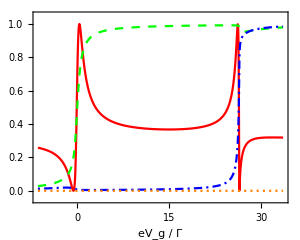

```mathematica
ListPlot[{L1,L2,L3,L4},
FrameLabel->{"eV_g / Γ",""},
AxesOrigin-> {-0.16/Γ,0},
PlotRange->{-0.05,1.05},
AspectRatio->0.8,
Frame->True,
Joined->True,
ImageSize->300,
PlotStyle->{{RGBColor[1,0,0]},
{RGBColor[0,1,0],Dashing[{0.02,0.02}]},
{RGBColor[0,0,1],Dashing[{0.005,0.01,0.02,0.01}]},
{RGBColor[1,0.5,0],Dashing[{0.005,0.01}]}},
PlotLegend->{"G/(e^2/ h)","<n_1>","<n_2>","Cov(n_1,n_2)"},
LegendPosition->{-0.25,0.16},
LegendSize->{0.6,0.4},
LegendTextSpace->2.7,
LegendBorder->Black,
LegendShadow->None]
```